```mathematica
f[x_]:=Piecewise[{{Interpolation[{{-8,2},{-5,1},{-2,-2},{0,1}},InterpolationOrder->1][x],-8<=x<=0},{Sqrt[1-(x-1)^2]+1,0<x<=2},{1-Sqrt[1-(x-3)^2],2<x<=4},{-1/(x-5),4<x<4.99},{Log[x-5],x>5.01}},Undefined]
```

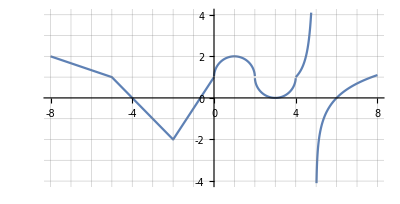

```mathematica
Plot[f[x],{x,-8,8},AspectRatio->Automatic,Ticks->{Range[-8,8],Range[-4,4]},PlotRange->{-4.1,4.1},GridLines->{Range[-8,8],Range[-4,4]},PlotPoints->200]
```

```mathematica
hh=Hold
```

Hold

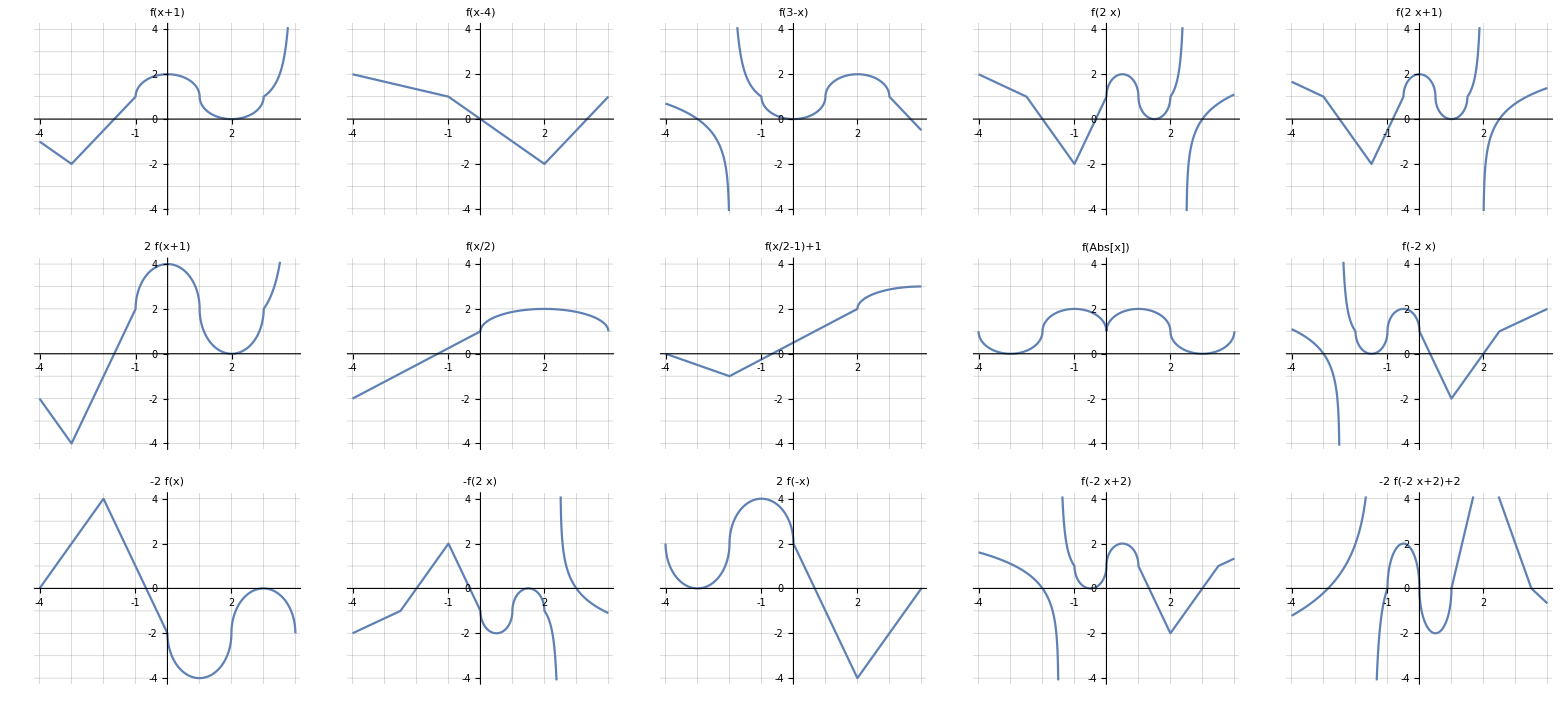

```mathematica
Partition[Plot[#,{x,-4,4},AspectRatio->Automatic,Ticks->{Range[-4,4],Range[-4,4]},PlotRange->{-4.1,4.1},GridLines->{Range[-4,4],Range[-4,4]},PlotPoints->200,PlotLabel->HoldForm[#],Exclusions->Automatic]&/@{hh[f[x+1]],hh[f[x-4]],hh[f[3-x]],hh[f[2x]],hh[f[2x+1]],hh[2f[x+1]],hh[f[1/2 x]],hh[f[1/2x-1]+1],hh[f[Abs[x]]],hh[f[-2x]],hh[-2f[x]],hh[-f[2x]],hh[2f[-x]],hh[f[-2x+2]],hh[-2f[-2x+2]+2]},5]//TableForm
```